## AbstractCategory ReducedMorphismAssociation

Here, y•f = h•(g•f) = h•x, but the older ResourceFunction[“AbstractCategory”] doesn’t know this (some morphisms appear double) because it can’t handle non-elementary composition equivalences.

<|f→a->b,g→b->c,h→c->d,i→d->e,x→a->c,y→b->d,y⊙f→a->d,i⊙h→c->e,h⊙x→a->d,i⊙y→b->e,(i⊙y)⊙f→a->e,(i⊙h)⊙g→b->e,(i⊙h)⊙x→a->e,ã→a->a,b̃→b->b,c̃→c->c,d̃→d->d,ẽ→e->e|>

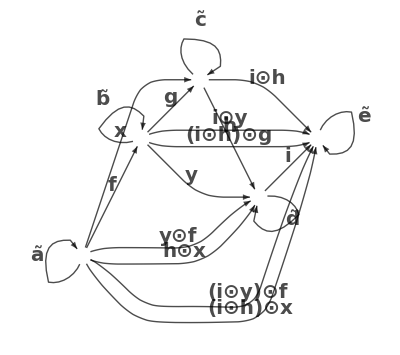

```mathematica
cat=ResourceFunction["AbstractCategory"][<|f->{a,b},g->{b,c},h->{c,d},i->{d,e},x->{a,c},y->{b,d}|>,{},{CircleDot[g,f]==x,CircleDot[h,g]==y}];
cat["ReducedMorphismAssociation"]
cat["ReducedLabeledGraph"]
```

{f→a->b,g→b->c,h→c->d,i→d->e,x→a->c,h⊙g→b->d,(h⊙g)⊙f→a->d,i⊙h→c->e,i⊙y→b->e,i⊙(h⊙(g⊙f))→a->e,ã→a->a,b̃→b->b,c̃→c->c,d̃→d->d,ẽ→e->e}

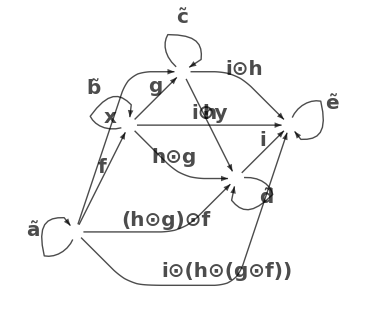

```mathematica
cat=AbstractCategory[<|f->{a,b},g->{b,c},h->{c,d},i->{d,e},x->{a,c},y->{b,d}|>,{},{CircleDot[g,f]==x,CircleDot[h,g]==y}];
cat["ReducedMorphismAssociation"]
cat["ReducedLabeledGraph"]
```

ReducedMorphismAssociation still treats no two morphisms as equivalent a priori when objects are reduced, except for identities, which get merged too.

AbstractCategory[…]

{f→A2->B3,g→B3->B3,h→A2->B3,i→B3->B3,g⊙f→A2->B3,i⊙g→B3->B3,i⊙h→A2->B3,i⊙(g⊙f)→A2->B3,OverTilde[A2]→A2->A2,OverTilde[B3]→B3->B3}

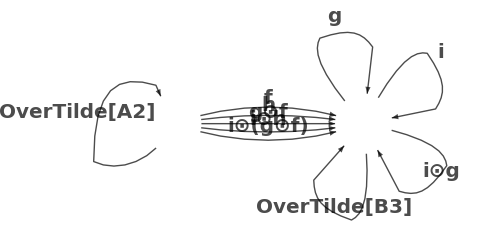

```mathematica
cat2=AbstractCategory[<|f->{A,B},g->{B,B2},h->{A2,B2},i->{B2,B3}|>,{A==A2,B==B2,B3==B2}]
cat2["ReducedMorphismAssociation"]
cat2["ReducedLabeledGraph"]
```

Compatibility with CommutativityEquations (if they are correct anyway):

```mathematica
cEq=cat2["ReducedCommutativityEquations"]
```

{f==h,f==g⊙f,f==i⊙h,f==(i⊙g)⊙f,g==i,g==i⊙g,g==OverTilde[B2]}

AbstractCategory[…]

{i⊙(g⊙f)→A2->B3,OverTilde[B3]→B3->B3,OverTilde[A2]→A2->A2}

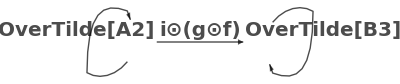

```mathematica
cat3=AbstractCategory[<|f->{A,B},g->{B,B2},h->{A2,B2},i->{B2,B3}|>,{A==A2,B==B2,B3==B2},cEq]
cat3["ReducedMorphismAssociation"]
cat3["ReducedLabeledGraph"]
```

Functor test from Issue #4 (make sure to use the updated AbstractFunctor code, which uses the new AbstractCategory):

```mathematica
cat=AbstractCategory[<|f->{U,V},g->{V,X},h->{Y,X},i->{X,Z}|>];
func=AbstractFunctor[cat,<|U->A,Y->A2,V->B,X->B2,Z->B3|>,<||>,{},<||>,CircleDot,OverTilde,{A==A2,B==B2,B2==B3},{CircleDot[g,f]==f,CircleDot[i,h]==h,h==f,CircleDot[i,g]==OverTilde[B3],g==OverTilde[B3],i==OverTilde[B3]}];
func["CodomainCategory"]["ReducedMorphismAssociation"]
func["CodomainCategory"]["ReducedLabeledGraph"]
```

{i⊙(g⊙f)→A2->B3,OverTilde[B3]→B3->B3,OverTilde[A2]→A2->A2}

-Graphics-

<|f→A2->B3,OverTilde[B3]→B3->B3,OverTilde[B3]⊙f→A2->B3,OverTilde[A2]→A2->A2|>

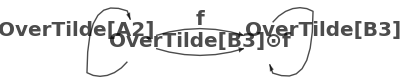

```mathematica
cat=ResourceFunction["AbstractCategory"][<|f->{U,V},g->{V,X},h->{Y,X},i->{X,Z}|>];
func=ResourceFunction["AbstractFunctor"][cat,<|U->A,Y->A2,V->B,X->B2,Z->B3|>,<||>,{},<||>,CircleDot,OverTilde,{A==A2,B==B2,B2==B3},{CircleDot[g,f]==f,CircleDot[i,h]==h,h==f,CircleDot[i,g]==OverTilde[B3],g==OverTilde[B3],i==OverTilde[B3]}];
func["CodomainCategory"]["ReducedMorphismAssociation"]
func["CodomainCategory"]["ReducedLabeledGraph"]
```